```mathematica
(* 03/31/10 : Visualize the HG modes :
  Generate the HG modes with appropriate waist at z=0.
04/12/10 : Automate the filename creation.
04/27/10 : Parameterize the constant Mx also.
*)
```

```mathematica
Clear[Evaluate[Context[]<>"*"]]
P = 50; L = 25; A0SX = N[25 Sqrt[2]];76.5;49.5495;62.0621;32.1572;  a0sx = A0SX/10^6;
(* Visualize HG mode mx at the z=0, so all exponetial phases are 0 *)
LGmode[p_,l_,pts_,a0sy_]:=Module[{},
LaguerreL[p,Abs[l],pts^2/a0sy^2] Exp[-pts^2/(2 a0sy^2)] If[Abs[l]>0,(pts/a0sy)^Abs[l],1] Sqrt[Factorial[p]/(Pi*Factorial[p+Abs[l]])]/a0sy];
(* Use memoization to save time & memory *)
Npts =500; rmax = 1.6*10^-3; dr = rmax/Npts;pts = Range[0,rmax,dr];
LGmodeX = {};
For[l = 0,l<L,l = l+1,
For[p = 0,p<P,p=p+1,
tmp = LGmode[p,l,pts,a0sx];
LGmodeX =Append[LGmodeX,tmp];
]];
Export[StringJoin["./SlaguerreX",ToString[P],"_",ToString[L],"_",ToString[A0SX],".dat"],MatrixForm[LGmodeX]]
(*ListDensityPlot[Abs[HGmodeX]^2]*)
```

./SlaguerreX50_25_35.3553.dat

```mathematica
Table[ListPlot[LGmode[p,0,pts,a0px]],{p,0,10}]
```

```mathematica
LGmode[p_,l_,pts_,a0sy_]:=Module[{},
LaguerreL[p,Abs[l],pts^2/a0sy^2] Exp[-pts^2/(2 a0sy^2)] If[Abs[l]>0,(pts/a0sy)^Abs[l],1] Sqrt[Factorial[p]/(Pi*Factorial[p+Abs[l]])]/a0sy];
LGmode[p,0,pts,a0sy]
```

(ⅇ^(-pts^2/(2 a0sy^2)) LaguerreL[p,pts^2/a0sy^2])/(a0sy √π)

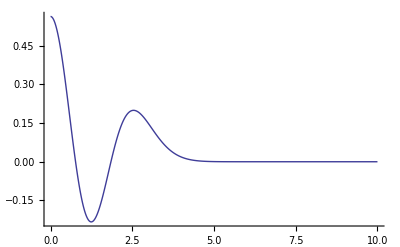

```mathematica
ListPlot[Table[{x,LGmode[2,0,x,1]},{x,0,10,0.01}],Joined->True,PlotRange->All]
```

```mathematica
N[LaguerreL[2,0,x]]
ListPlot[Table[LaguerreL[2,0,x],{x,0,10,0.1}]]
```

```mathematica
100 Sqrt[2]//N
```

141.421